Causality Constraints on Massive Gravity (1610.02033)

X.O. Camanho, G.L. Gómez, R. Rahman, 
Causality Constraints on Massive Gravity
https://arxiv.org/abs/1610.02033

#### Definitions

The Minkowski null frame and its inverse:

```mathematica
η=({{0, -1, 0}, {-1, 0, 0}, {0, 0, 1}});
iη=Inverse@η;  iη//MatrixForm
```

(0 | -1 | 0
-1 | 0 | 0
0 | 0 | 1)

The vielbien of g:

```mathematica
Ε=({{-F/2, 1, 0}, {1, -G/2, 0}, {0, 0, 1}});
```

The metric g and its null cone:

```mathematica
g=Transpose[Ε].η.Ε;
g//MatrixForm
```

(F | -1-(F G)/4 | 0
-1-(F G)/4 | G | 0
0 | 0 | 1)

```mathematica
nc$g=({{𝕋u,𝕋v,𝕋r}}.g.Transpose[{{𝕋u,𝕋v,𝕋r}}])⟦1,1⟧//Simplify
```

𝕋r^2+1/2 (F 𝕋u-2 𝕋v) (2 𝕋u-G 𝕋v)

The inverse vielbien:

```mathematica
itΕ=Inverse@Transpose@Ε//Simplify;
itΕ//MatrixForm
```

((2 G)/(4-F G) | 4/(4-F G) | 0
4/(4-F G) | (2 F)/(4-F G) | 0
0 | 0 | 1)

```mathematica
BesselK[0,10.^-30]
```

69.1935

The particular field F for the sandwich pp-wave solution:

```mathematica
A[u_,a_,λ_]:=Piecewise[{{a Exp[-(λ^2 u^2)/((u^2-λ^2)^2)], -λ<u<λ}, {0, True}}]
```

-Graphics-

```mathematica
Fg[u_,r_,a_,λ_,m_]:=A[u,a,λ]Piecewise[{{BesselK[0,m Abs@r], m Abs@r≥10^-30}, {70, True}}]
```

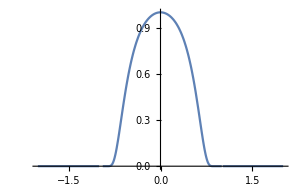
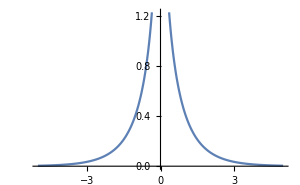

```mathematica
Row@{Plot[A[u,1,1],{u,-2,2},ImageSize->300],Plot[BesselK[0,Abs@r],{r,-5,5},ImageSize->300]}
```

The null cone of g:

#### Null cone field and null geodesics

```mathematica
ncEllipsed[loc_,lVec_,nVec_,bθ_,scale_]:=With[
{l=Normalize@lVec,n=Normalize@nVec},
With[
{
a = Norm[ l - n ],
c = Norm[ l + n ],
b = Sin[bθ] scale
},
With[
{p1 = (a √(c^2-b^2))/c,p2 = (c^2-b^2)/c},
	Translate[Rotate[Scale[
{
Line[{{-p1,p2},{0,0},{p1,p2}}],
Line[{{-p1,-p2},{0,0},{p1,-p2}}],
Thick, Circle[{0,c},{a,b}],
Circle[{0,-c},{a,b},MinMax@{π-bθ/2,2π+bθ/2}],
Thin,Dashed,Circle[{0,-c},{a,b},MinMax@{bθ/2,π-bθ/2}]
},
scale ], {{0,1},(l+ n )/2}],loc]
]]]
```

```mathematica
uiConeField[a_,λ_,m_,x_,r_,zt_,range_:1.5,extraPanel_:False,in3D_:False]:=Block[
{F,G,lVec,nVec,nc,tvec$g,scale=range/1.5},
F= Fg[N@u,N[x r],N@a,N@λ,N@m];
G=Fg[N@v,N[(1-x)r],N@a,N@λ,N@m];
lVec[z_,t_]={#⟦2⟧-#⟦1⟧,#⟦1⟧+#⟦2⟧}/2^(1/2)&@(itΕ⟦1,{1,2}⟧/.{u->(t-z)/2^(1/2),v->(t+z)/2^(1/2)});
nVec[z_,t_]={#⟦2⟧-#⟦1⟧,#⟦1⟧+#⟦2⟧}/2^(1/2)&@(itΕ⟦2,{1,2}⟧/.{u->(t-z)/2^(1/2),v->(t+z)/2^(1/2)});
nc=nc$g/.{u->(zt⟦2⟧-zt⟦1⟧)/2^(1/2),v->(zt⟦2⟧+zt⟦1⟧)/2^(1/2)};
tvec$g=Normalize[ Normalize@itΕ⟦1⟧ + Normalize@itΕ⟦2⟧ ]/.{u->(zt⟦2⟧-zt⟦1⟧)/2^(1/2),v->(zt⟦2⟧+zt⟦1⟧)/2^(1/2)};
Row@{
Show[
StreamPlot[lVec[z$v,t$v],{z$v,-2range,2range},{t$v,-2range,2range},
StreamStyle->{Opacity[0.5],Blue,"Line"},
StreamPoints->ControlActive[{{0,0}},{
Table[{-u/2,u/2},{u,-2range,2range,range/3}],
0.1,5range}],
ImageSize->{350,350}
],
StreamPlot[nVec[z$v,t$v],{z$v,-2range,2range},{t$v,-2range,2range},
StreamStyle->{Opacity[0.5],Red,"Line"},
StreamPoints->ControlActive[{{0,0}},{
Table[{v/2,v/2},{v,-2range,2range,range/3}],
0.1,5range}]
],
Graphics[{
Arrow[{zt,zt+0.6{1,1}scale}],Text[Style[v,15],zt+0.7{0.9,0.7}scale],
Arrow[{zt,zt+0.6{-1,1}scale}],Text[Style[u,15],zt+0.7{-0.9,0.7}scale],
ncEllipsed[zt,lVec@@zt,nVec@@zt,0.35/scale,0.3scale],
Blue,Arrow[{zt,zt+0.3Normalize[lVec@@zt]scale}],
Red,Arrow[{zt,zt+0.3Normalize[nVec@@zt]scale}],
Black,
Text[Style["z ⟶",15],Scaled@{0.87,0.038}],
Text[Style[Rotate["t  ⟶",90Degree],15],Scaled@{0.04,0.87}],
If[extraPanel,Locator@zt,Point@zt]
}],
PlotRange->range,
Frame->True,BaseStyle->{FontFamily->"Cambria",12}
],
Sequence@@If[¬extraPanel,{Nothing},{
Spacer[20],
If[in3D,Graphics3D[
GeometricTransformation[ContourPlot3D[
nc,
{𝕋v,-1,1},
{𝕋r,-1,1},
{𝕋u,-1,1},
PlotPoints->ControlActive[10,50],
Mesh->None,Contours->{0},ContourStyle->{White,Opacity[0.9],Specularity[1,20]},
Boxed->False,Axes->False,
RegionFunction->Function [ {vv,rr,uu}, Abs[ {uu,vv,rr}.tvec$g ] ≤0.7]
]⟦1⟧,RotationMatrix[-45Degree,{0,1,0}]],
Boxed->False,Axes->False,
AxesLabel->{Row@{z,"  ⟶"},None,Rotate[Row@{t,"  ⟶"},90Degree]},Ticks->None,PlotRange->All,
BaseStyle->{FontFamily->"Cambria",Bold,15},
ImageSize->{350,300},ViewPoint->Front
],
Graphics[{
Gray,
Arrow[0.7{{-1,-1},{1,1}}],Text[Style[v,15],0.8{0.88,0.75}],
Arrow[0.7{{1,-1},{-1,1}}],Text[Style[u,15],0.8{-0.88,0.75}],
Black,
Arrow[0.9{{0,-1},{0,1}}],Text[Style[t,15],{-0.07,0.82}],
Arrow[0.9{{-1,0},{1,0}}],Text[Style[z,15],{0.82,-0.07}],
ncEllipsed[{0,0},lVec@@zt,nVec@@zt,0.2,0.4],
Blue,
Arrow[{{0,0},0.3Normalize[lVec@@zt]}],
Text[Style[ℓ,15],0.3RotationMatrix[-10Degree].Normalize[lVec@@zt]],
Red,
Arrow[{{0,0},0.3Normalize[nVec@@zt]}],
Text[Style[𝓃,15],0.3RotationMatrix[10Degree].Normalize[nVec@@zt]]
},
PlotRange->1,
BaseStyle->{FontFamily->"Cambria",12},
ImageSize->350
]
]}
]
}]
```

```mathematica
Manipulate[
uiConeField[a,λ,m,x,r,zt,zoom,True,in3D],
Panel[Grid[{
{
Control[{{zt,{0,0}},Locator,Appearance->None}];Spacer[10],
"a",
Control[{{a,0.93,""},-0.93,0.93}],
Spacer[10],
"x",Control[{{x,0.01,""},0.001,0.999}],
Spacer[10],
"3D",Control[{{in3D,False,""},{True,False}}]
},
{
"",
"λ",Control[{{λ,1,""},0.1,1.5}],
"",
"r",Control[{{r,10,""},0.5,10}],
"",
"",Button["▶",
Block[{F,G},
F= Fg[N@u,N[x r],N@a,N@λ,N@m];
G=Fg[N@v,N[(1-x)r],N@a,N@λ,N@m];
Do[
zt=zt+0.01{#⟦2⟧-#⟦1⟧,#⟦1⟧+#⟦2⟧}/2^(1/2)&@(itΕ⟦2,{1,2}⟧/.{u->(zt⟦2⟧-zt⟦1⟧)/2^(1/2),v->(zt⟦2⟧+zt⟦1⟧)/2^(1/2)}),
{30}
]
],
Method->"Queued"]
},
{
"",
"m",Control[{{m,1,""},0.5,1.5}],
"","zoom:",Control[{{zoom,1.5,""},1.5,10,0.5}]
}
},Alignment->Left],ImageSize->Scaled[1],BaseStyle->{FontFamily->"Cambria",FontSize->14}],
SaveDefinitions->True,Deployed->True,AppearanceElements->None,Paneled->False,
FrameMargins->0
]
```

#### Scattering on pp-waves

```mathematica
ticks[min_,max_]:=Join[Table[{i,Style[i,12],{.01,0}},{i,Ceiling[min],Floor[max]}],Table[{j+.5,,{.005,0}},{j,Round[min],Round[max-1],1}]]
```

```mathematica
particlePosition[t_,δ_,r$sep_,b$sep_]:=If[t≤-2.5,
{-δ-t,-r$sep/2+b$sep,0},
If[ t≤0.5,
{-δ+2.5,-r$sep/2+b$sep+(t+2.5),0},
If[t≤3,
{-δ+2.5+(t-0.5),r$sep/2-b$sep,0},
{-δ+5,r$sep/2-b$sep-(t-3),0}
]
]
]
```

```mathematica
particleTime[t_,δ_,r$sep_,b$sep_]:=t
```

```mathematica
With[
{r$sep=4,b$sep=1/2,δ=5},
Manipulate[
Row@{
Show[
Graphics3D[{
If[$ControlActiveSetting,Nothing,{
Arrowheads[{-0.024,0.024}],
Gray,Arrow@{{1,-r$sep/2,0},{1,r$sep/2,0}},
Black,Text[Style[r,15],{1,0,0.4}],
Gray,Arrow@{{0.5,-r$sep/2+b$sep,0},{0.5,r$sep/2-b$sep,0}},
Black,Text[Style[d,15],{0.5,0,0.4}],
Arrowheads[0.015],
Gray,Arrow@{{-1,-r$sep/2+b$sep+0.5,0},{-1,-r$sep/2+b$sep,0}},
Arrow@{{-1,-r$sep/2-0.5,0},{-1,-r$sep/2,0}},
Black,Text[Style[b,15],{-1,-r$sep/2+b$sep/2,0.1}]
}],
Arrowheads[0.024],
If[t<-2.5,Gray,LightGray],
Arrow@{{0,-r$sep/2+b$sep,0},{-δ+2.5,-r$sep/2+b$sep,0}},
If[-2.5≤t<0.5,Gray,LightGray],
Arrow@{{-δ+2.5,-r$sep/2+b$sep,0},{-δ+2.5,r$sep/2-b$sep,0}},
If[0.5≤t<3,Gray,LightGray],
Arrow@{{-δ+2.5,r$sep/2-b$sep,0},{0,r$sep/2-b$sep,0}},
If[3<t,Gray,LightGray],
Arrow@{{0,r$sep/2-b$sep,0},{0,-r$sep/2+b$sep,0}},
Arrowheads[0.024],Opacity[0.35],Specularity[1,20],
Blue,Arrow@Tube@{{-δ,-r$sep/2,0},{δ,-r$sep/2,0}},
Red,Arrow@Tube@{{δ,r$sep/2,0},{-δ,r$sep/2,0}},
(* Particle *)
Opacity[0.5],Specularity[1,20],Gray,
Sphere[particlePosition[t,δ,r$sep,b$sep],0.2],
Sphere[{particlePosition[t,δ,r$sep,b$sep]⟦1⟧,δ-0.1,0.2},0.1]
},
PlotRange->{{-δ,δ},{-δ,δ},{-δ,δ}/2},
Boxed->True,Axes->True,AxesLabel->(Style[#,15]&/@{z,x,y}),
FaceGrids->{{{-1,0,0},{Range[-δ,δ,0.5],Range[-δ,δ,0.5]}}},
FaceGridsStyle->Directive[Dashed,LightGray],
BaseStyle->{FontFamily->"Cambria",FontSize->14},
Ticks->{ticks[-δ,δ],ticks[-δ,δ],ticks[-δ,δ]},
ImageSize->600
],
SliceDensityPlot3D[   (* F[u], moving along v *)
Abs@Fg[(*u*) (t-z)/2^(1/2)+2,((x+r$sep/2)^2+y^2)^(1/2),a,λ,m],
ControlActive[{(t-z)/2^(1/2)+2==0},{Thread[(t-z)/2^(1/2)+2==Subdivide[-2/3λ,2/3λ,6]]}],
{z,-δ,δ},
{x,-δ,δ},
{y,-δ,δ},
PlotRange->{0.1,5},BoundaryStyle->None,
ColorFunction->(Directive[Blue,Opacity@Rescale[#,{0.1,1},{0.15,0.9}]]&)
],
SliceDensityPlot3D[  (* F[v], moving along u *)
Abs@Fg[(*v*) (t+z)/2^(1/2),((x-r$sep/2)^2+y^2)^(1/2),a,λ,m],
ControlActive[{(t+z)/2^(1/2)==0},{Thread[(t+z)/2^(1/2)==Subdivide[-2/3λ,2/3λ,6]]}],
{z,-δ,δ},
{x,-δ,δ},
{y,-δ,δ},
PlotRange->{0.1,5},BoundaryStyle->None,
ColorFunction->(Directive[Red,Opacity@Rescale[#,{0.1,1},{0.15,0.9}]]&)
],
ParametricPlot3D[
{
{z,δ,A[(t-z)/2^(1/2)+2,a,λ]}, (* u *)
{z,δ-0.1,A[(t+z)/2^(1/2),a,λ]} (* v *)
},
{z,-δ,δ},
PlotStyle->{{Opacity[0.5],Blue},{Opacity[0.5],Red}}
]
],
Spacer[20],
Show[
uiConeField[a,λ,m,0.01,10,{particlePosition[t,δ,r$sep,b$sep]⟦1⟧,t},6][[1,1]],
ParametricPlot[
{
{z,t+A[t-z,a,λ]}, (* u *)
{z,t+A[t+z,a,λ]} (* v *)
},
{z$v,-δ,δ},
Epilog->{PointSize[0.1],Point[{
particlePosition[t,δ,r$sep,b$sep]⟦1⟧,particleTime[t,δ,r$sep,b$sep]
}]
},
PlotRange->{{-δ,δ},{-δ,δ+1}},
PlotStyle->{{Opacity[0.5],Blue},{Opacity[0.5],Red}},
BaseStyle->{FontFamily->"Cambria",12},
FrameLabel->{Style[Row@{z," ⟶"},15,Darker@Green],Style[Row@{time,"  ⟶"},15,Darker@Green]},
Frame->True,AspectRatio->1,
ImageSize->400
]
]
},
Panel@Row[{
Column@{
Control[{{a,0.93},-0.93,0.93}],
Control[{{λ,1},0.1,1.5}],
Control[{{m,1},0.5,1.5}]
},
Spacer[20],
Column@{
Control[{{t,-δ},-δ,δ+1,0.1,AnimationRate->1/5,Appearance->"Open"}]
}
}],
SaveDefinitions->True,AppearanceElements->None,Paneled->False
]
]
```

```mathematica
particleTime2[t_,δ_,r$sep_,b$sep_]:=If[t≤-3,t,
If[ t≤-2.5,-3-(t+3),
If[t≤1,-4+(t+2.5),
If[t≤2,
0-(t-1),
0+(t-2)
]
]
]
]
```